# Signal Processing - Project 1

## William Lewin & Elias Chahine wlewin@kth.se echahine@kth.se

## Part 1

### Assignment

A mobile station is moving along a straight line, away from a basestation at position x=0. The basestation antenna is at 30m above the ground and the mobile antenna is at 1.5 m. As seen by the picture the mobile is receiving two signals one direct ray and one reflected. Assume that the reflection is perfect which means no power loss at the reflection, but a phase shift of π.

Plot the squared amplitude (power) of the received signal when the mobile is moving from position x=0 to x=2km. Experiment with different types of graphs (e.g. log-scale, dB etc) to get a nice picture.

### Discussion

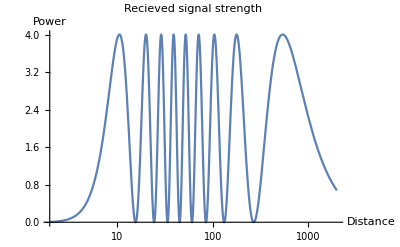
The problem at hand is to examine the effect of line-of-sight propagation of wireless signals.

When the car travels from 0 to 2000m away from the antenna, both the reflected and the direct signal changes. 

The recieved signal can be interpereted as the sum of both the reflected and the direct signal.

The following plot is a representation of both the reflected and the direct signal.

-Graphics-

### Code

```mathematica
ClearAll["`*"]
f=900*10^6; (*Frequency*)
c=299792458; (*Speed of light*)
ω=2*Pi*f;
th=30; (*Tower height*)
ch=1.5; (*Height of the car-antenna*)

(*Pythagoran theorem*)

(*Direct from tower to car: *)
distance1[x_]:=√((th-ch)^2+x^2);
(*Reflected from tower to car: *)
distance2[x_]:=√((th+ch)^2+x^2);


(* Time taken for the signal to reach the car at both signals *)
time1[x_]=distance1[x]/c;
time2[x_]= distance2[x]/c;
(*Direct signal*)
signal1[t_]:=ⅇ^(ⅉ(ω*t)); 
(*Reflected signal, Phase shifted direct signal*)
signal2[t_]:=ⅇ^(ⅉ(ω*t+Pi)); 

(*Recieved signal, from assignment*)
recieved[t_, x_]:=signal1[t-time1[x]]+signal2[t-time2[x]] ;

(*Remove imaginary part from signal*)
remove[x_]:=Simplify[ExpandAll[ⅇ^(-ⅉ*ω*t)recieved[t,x]]];
amplitude[x_]:=(Abs[remove[x]])^2;
LogLinearPlot[amplitude[x],{x,0,2000}, PlotLabel->"Recieved signal strength", AxesLabel->{"Distance", "Power"}]
```

-Graphics-

## Part 2

### Assignment

In this problem you shall examine the effect of sampling. Study the signal x[t_]:=Abs[Sin[2π f0 t]] where f_0=220Hz. 

Use the method Play and explain the sound by studying the complex FourierSeries.

Play the sound using the sampling frequency 8000Hz,What are the frequencies you will hear?

Play the sound using the sampling frequency 1000Hz. What frequencies will you hear now?

Draw the correct spectrum in these two cases.

### Discussion

### Code

```mathematica
ClearAll["`*"]
f=220;
t0=1/f;
SetOptions[{FourierCoefficient,FourierSeries},FourierParameters:> {1,2*Pi/t0}];
```

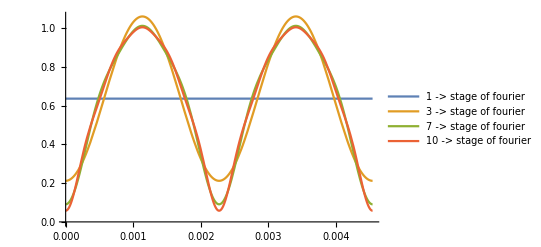

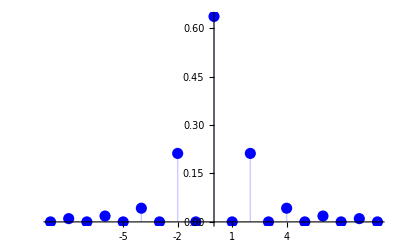

```mathematica
(*Orginal assignement function*)
org[t_]:=Abs[Sin[2*Pi*f*t]];
(*Representing the function as a sum of sine waves*)
orgSeries[t_,k_]:=FourierSeries[org[t],t,k]
(*The graph shows that the higher the grade of a fourier series, the more accurate the plot becomes*)
Plot[{Evaluate[orgSeries[t,1]],Evaluate[orgSeries[t,3]],Evaluate[orgSeries[t,7]],Evaluate[orgSeries[t,10]]},{t,0,t0}, PlotLegends->{"1 -> stage of fourier" ,"3 -> stage of fourier","7 -> stage of fourier","10 -> stage of fourier"}]
orgCoe[k_]:=FourierCoefficient[org[t],t,k]
DiscretePlot[Abs[orgCoe[k]],{k,-9,9},Ticks->{Range[-5,5],Automatic},PlotRange->All,PlotStyle->Directive[PointSize[0.02],Thick,Blue]]
```

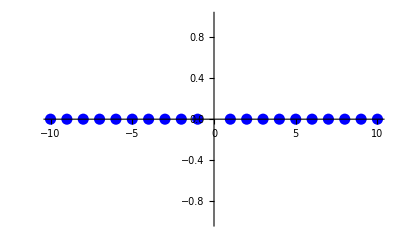

```mathematica
(*1000 Hz*)
s1k[t_]:=Abs[Sin[(2*Pi*f*t)/1000]];
s1kSeries[t_,k_]:=FourierSeries[s1k[t],t,k]
s1kCoe[k_]:=FourierCoefficient[s1kSeries[k],t,k]
DiscretePlot[s1kCoe[k],{k,-10,10},PlotRange->All,PlotStyle->Directive[PointSize[0.02],Thick,Blue]]
```